{2,5}

{3,6}

{5,7}

{10,8}

{24,9}

{74,10}

{307,11}

{1556,12}

{9151,13}

```mathematica
Table[dops2[[i]],{i,Range[5,9]}]
```

{{24,96},{24,120},{24,24},{96,120},{24,24}}

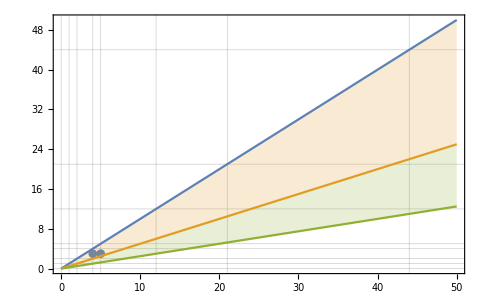

```mathematica
With[
{range=50},
Show[
ListPlot[Select[Table[dops2[[i]],{i,Range[10,23]}],#[[2]]<#[[1]]&]/24,PlotRange->{{0,range},{0,range}},PlotMarkers->Automatic],
Plot[{x,1/2*x,1/4*x},{x,0,range},  Filling->{2->{1},3->{2}}], Frame->True, GridLines->{Jacobsthal,Jacobsthal},
ImageSize->500
]
]
```

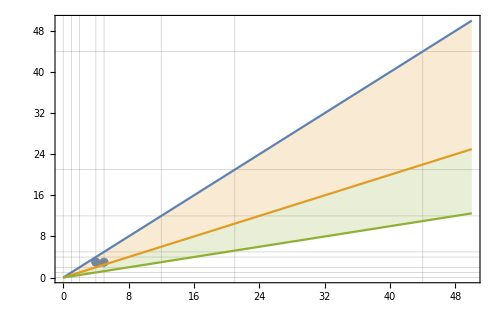

```mathematica
With[
{range=50},
Show[
ListPlot[Select[Table[dops2[[i]],{i,Range[24,73]}],#[[2]]<#[[1]]&]/24,PlotRange->{{0,range},{0,range}},PlotMarkers->Automatic],
Plot[{x,1/2*x,1/4*x},{x,0,range},  Filling->{2->{1},3->{2}}], Frame->True, GridLines->{Jacobsthal,Jacobsthal},
ImageSize->500
]
]
```

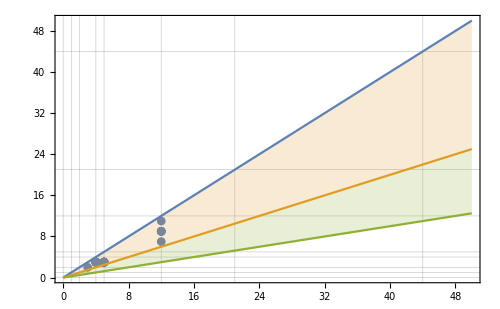

```mathematica
With[
{range=50},
Show[
ListPlot[Select[Table[dops2[[i]],{i,Range[74,306]}],#[[2]]<#[[1]]&]/24,PlotRange->{{0,range},{0,range}},PlotMarkers->Automatic],
Plot[{x,1/2*x,1/4*x},{x,0,range},  Filling->{2->{1},3->{2}}], Frame->True, GridLines->{Jacobsthal,Jacobsthal},
ImageSize->500
]
]
```

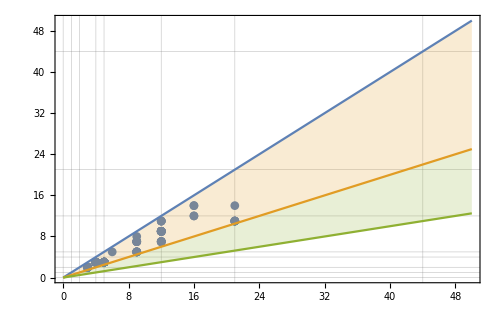

```mathematica
With[
{range=50},
Show[
ListPlot[Select[Table[dops2[[i]],{i,Range[307,1555]}],#[[2]]<#[[1]]&]/24,PlotRange->{{0,range},{0,range}},PlotMarkers->Automatic],
Plot[{x,1/2*x,1/4*x},{x,0,range},  Filling->{2->{1},3->{2}}], Frame->True, GridLines->{Jacobsthal,Jacobsthal},
ImageSize->500
]
]
```

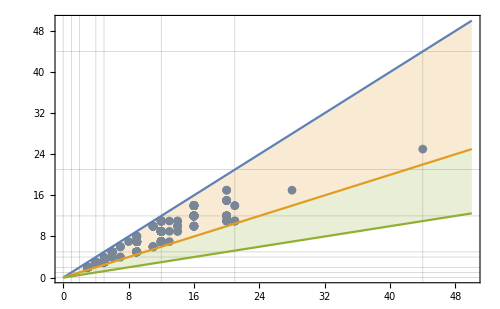

```mathematica
With[
{range=50},
Show[
ListPlot[Select[Table[dops2[[i]],{i,Range[1556,9150]}],#[[2]]<#[[1]]&]/24,PlotRange->{{0,range},{0,range}},PlotMarkers->Automatic],
Plot[{x,1/2*x,1/4*x},{x,0,range},  Filling->{2->{1},3->{2}}], Frame->True, GridLines->{Jacobsthal,Jacobsthal},
ImageSize->500
]
]
```

```mathematica
SetDiff[large_,small_]:=Select[large,!MemberQ[small,#]&]
```

```mathematica
set4=DeleteDuplicates[Sort[Take[dops2,{10,23}]/24]]
```

{{1,1},{1,4},{1,5},{1,12},{4,3},{4,4},{4,5},{5,3},{5,12}}

```mathematica
set5=DeleteDuplicates[Sort[Take[dops2,{24,73}]/24]]
```

{{1,1},{1,4},{1,5},{1,12},{4,3},{4,4},{4,5},{4,9},{4,16},{5,3},{5,5},{5,6},{5,9},{5,12}}

```mathematica
set6=DeleteDuplicates[Sort[Take[dops2,{74,306}]/24]]
```

{{1,1},{1,4},{1,5},{1,12},{1,21},{3,2},{3,6},{3,9},{4,3},{4,4},{4,5},{4,9},{4,11},{4,16},{4,20},{5,3},{5,5},{5,6},{5,7},{5,9},{5,12},{5,20},{12,7},{12,9},{12,11},{12,12},{12,21}}

```mathematica
set6=Intersection[Sort[Take[dops2,{10,23}]/24],Sort[Take[dops2,{24,73}]/24]]
```

{{1,1},{1,4},{1,5},{1,12},{4,3},{4,4},{4,5},{5,3},{5,12}}

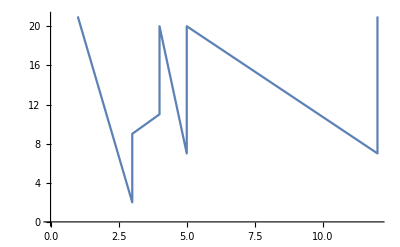

```mathematica
ListLinePlot[SetDiff[set6,set5]]
```

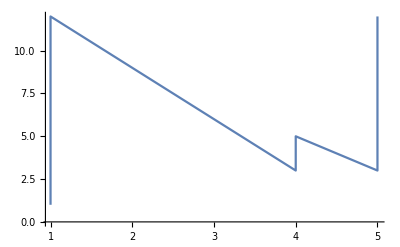

```mathematica
ListLinePlot[set4]
```

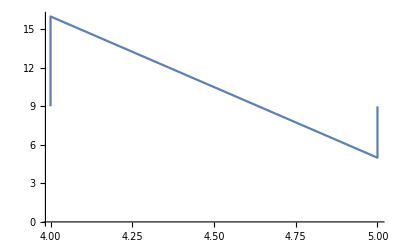

```mathematica
ListLinePlot[SetDiff[set5,set4]]
```

```mathematica
Sort[DeleteDuplicates[Select[Table[dops2[[i]],{i,Range[10,23]}],#[[2]]<#[[1]]&]/24]]
```

{{4,3},{5,3}}

```mathematica
Sort[DeleteDuplicates[Select[Table[dops2[[i]],{i,Range[24,73]}],#[[2]]<#[[1]]&]/24]]
```

{{4,3},{5,3}}

```mathematica
Sort[DeleteDuplicates[Select[Table[dops2[[i]],{i,Range[74,306]}],#[[2]]<#[[1]]&]/24]]
```

{{3,2},{4,3},{5,3},{12,7},{12,9},{12,11}}

```mathematica
Sort[DeleteDuplicates[Select[Table[dops2[[i]],{i,Range[307,1555]}],#[[2]]<#[[1]]&]/24]]
```

{{3,2},{4,3},{5,3},{6,5},{9,5},{9,7},{9,8},{12,7},{12,9},{12,11},{16,12},{16,14},{21,11},{21,14}}

```mathematica
Sort[DeleteDuplicates[Select[Table[dops2[[i]],{i,Range[1556,9150]}],#[[2]]<#[[1]]&]/24]]
```

{{3,2},{4,3},{5,3},{5,4},{6,4},{6,5},{7,4},{7,6},{8,7},{9,5},{9,7},{9,8},{11,6},{11,10},{12,7},{12,9},{12,11},{13,7},{13,9},{13,11},{14,9},{14,10},{14,11},{16,10},{16,12},{16,14},{20,11},{20,12},{20,15},{20,17},{21,11},{21,14},{28,17},{44,25}}

```mathematica
Sort[DeleteDuplicates[Select[Table[dops2[[i]],{i,Range[9151,100000]}],#[[2]]<#[[1]]&]/24]]
```

{{3,2},{4,3},{5,3},{5,4},{6,4},{6,5},{7,4},{7,5},{7,6},{8,5},{8,6},{8,7},{9,5},{9,6},{9,7},{9,8},{10,6},{10,7},{10,8},{10,9},{11,6},{11,7},{11,8},{11,9},{11,10},{12,7},{12,8},{12,9},{12,11},{13,7},{13,8},{13,9},{13,10},{13,11},{13,12},{14,8},{14,9},{14,10},{14,11},{14,13},{15,8},{15,9},{15,10},{15,11},{15,12},{15,14},{16,10},{16,11},{16,12},{16,13},{16,14},{16,15},{17,11},{17,13},{17,14},{17,15},{17,16},{19,10},{19,12},{19,14},{19,17},{20,11},{20,12},{20,15},{20,17},{20,19},{21,11},{21,12},{21,14},{21,15},{21,16},{21,18},{21,19},{21,20},{22,12},{22,13},{22,14},{22,15},{22,16},{22,17},{22,19},{22,21},{23,14},{23,16},{24,16},{24,18},{24,20},{25,13},{25,15},{25,16},{25,17},{25,19},{25,22},{25,23},{26,14},{26,16},{26,17},{26,18},{26,19},{26,20},{27,14},{27,16},{27,23},{27,26},{28,15},{28,17},{28,19},{28,21},{28,22},{28,23},{28,26},{29,15},{29,17},{29,18},{29,19},{29,20},{29,21},{29,23},{29,24},{30,17},{30,18},{30,19},{30,21},{30,25},{30,26},{33,17},{33,19},{33,21},{33,23},{33,25},{33,29},{33,31},{33,32},{36,19},{36,20},{36,23},{36,28},{36,31},{40,24},{40,26},{40,32},{40,34},{40,38},{41,21},{41,23},{41,34},{41,35},{41,38},{44,23},{44,25},{44,43},{45,25},{45,29},{45,32},{45,33},{45,35},{45,43},{48,26},{48,28},{48,30},{48,36},{48,44},{54,29},{54,30},{54,31},{54,33},{54,34},{54,35},{60,31},{60,36},{60,45},{60,49},{85,43}}

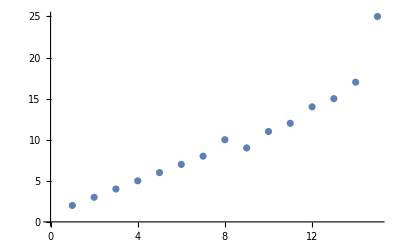

```mathematica
ListPlot[DeleteDuplicates[Map[Last[#]&,Sort[DeleteDuplicates[Select[Table[dops2[[i]],{i,Range[1556,9150]}],#[[2]]<#[[1]]&]/24]]
]]]
```

```mathematica
Count[deps1,1556<#[[2]]<9150&]
```

0